## 収束性のチェック

```mathematica
Clear["Global`*"]
(*NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
(*json="/Users/tomoaki/BEM/Goring1979_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)

jsonLINEAR="/Volumes/home/BEM/Goring1979/Goring1979_DT0d03_MESHwater0d09refined.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1_20250225/result.json"
(*jsonQUAD="/Volumes/home/BEM/Goring1979/Goring1979_DT0d03_MESHwater0d09refined.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_20250225/result.json"*)
(*jsonLINEAR="/Volumes/home/BEM/Goring1979/Goring1979_DT0d03_MESHwater0d08refined.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_20250225/result.json"*)
jsonLINEAR="/Volumes/home/BEM/benchmark20250501/Goring1979_DT0d05_MESHwater0d05refined.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json"
(*jsonLINEAR="/Users/tomoaki/BEM/Goring1979_DT0d03_MESHwater0d09refined.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_20250225/result.json"*)
jsonQUAD="/Volumes/home/BEM/benchmark20250501/Goring1979_DT0d05_MESHwater0d05refined.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1/result.json"
(*jsonLINEAR="/Users/tomoaki/BEM/Goring1979_DT0d03_MESHwater0d06refined.obj_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_20250225/result.json"
jsonQUAD="/Users/tomoaki/BEM/Goring1979_DT0d03_MESHwater0d06refined.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1_20250225/result.json"
*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_middle/result.json"*)
jsonInfo[jsonLINEAR]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

/Volumes/home/BEM/Goring1979/Goring1979_DT0d03_MESHwater0d09refined.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1_20250225/result.json

/Volumes/home/BEM/benchmark20250501/Goring1979_DT0d05_MESHwater0d05refined.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json

/Volumes/home/BEM/benchmark20250501/Goring1979_DT0d05_MESHwater0d05refined.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1/result.json

no. | title | length
1 | cpu_time | 597
2 | eq_of_motion | 597
3 | gauge1_intersection | 597
4 | gauge2_intersection | 597
5 | gauge3_intersection | 597
6 | gradPhi_worst_grad | 597
7 | gradPhi_worst_iteration | 597
8 | gradPhi_worst_value | 597
9 | simulation_time | 597
10 | wall_clock_time | 597
11 | water_E | 597
12 | water_EK | 597
13 | water_EP | 597
14 | water_face_size | 597
15 | water_point_size | 597
16 | water_volume | 597

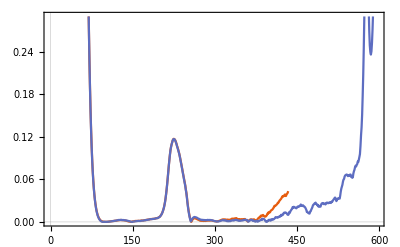

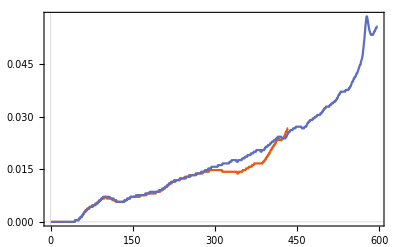

```mathematica
dataV0=importData[jsonQUAD,"water_EK"]+importData[jsonQUAD,"water_EP"];
dataV1=importData[jsonLINEAR,"water_EK"]+importData[jsonLINEAR,"water_EP"];
init=100;
ListPlot[100{Abs[dataV0/dataV0[[init]]-1],Abs[dataV1/dataV1[[init]]-1]},plot2Doption,PlotRange->All]

dataV0=importData[jsonQUAD,"water_volume"];
dataV1=importData[jsonLINEAR,"water_volume"];
init=1;
ListPlot[100{Abs[dataV0/dataV0[[init]]-1],Abs[dataV1/dataV1[[init]]-1]},plot2Doption,PlotRange->All]
```

```mathematica
getTFromLandDepth[150,180]
```

9.80169

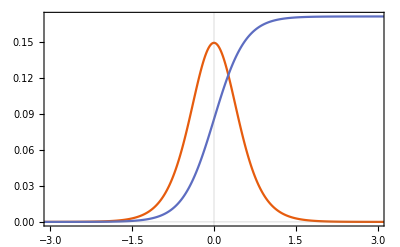

```mathematica
h=0.25;
H=0.1*h;
g=9.81;
c=Sqrt[g*(H+h)];
k=Sqrt[3*H/(4*h^3)];
eta[t_]:=H*Sech[k*(-c*(t))]^2

ListPlot[
{Table[{t,c*eta[t]/(h+eta[t])},{t,-5,5,0.01}],
Table[{t,NIntegrate[c*eta[T]/(h+eta[T]),{T,-Infinity,t}]},{t,-5,5,0.01}]},
PlotRange->{{-2/k*c,2/k*c},All},
Evaluate[plot2Doption]
]

(*ListPlot[
Table[{a,NIntegrate[c*eta[T]/(h+eta[T]),{T,-a/k*c,a/k*c}]},{a,0.5,5,0.1}],
PlotRange->All,
Evaluate[plot2Doption]
]*)
```

4.9

4.9

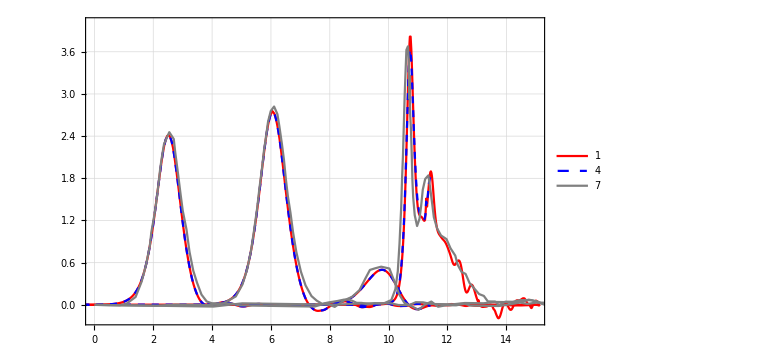

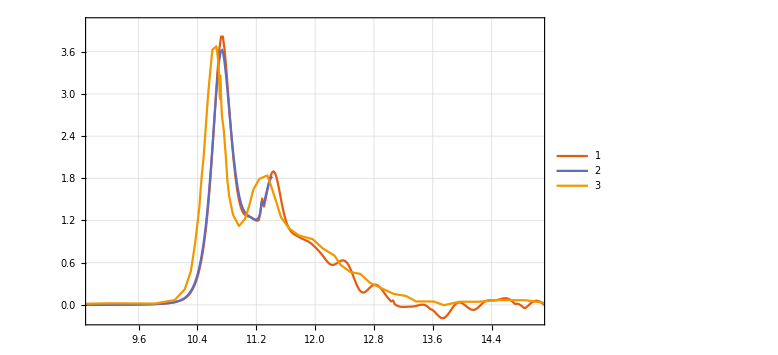

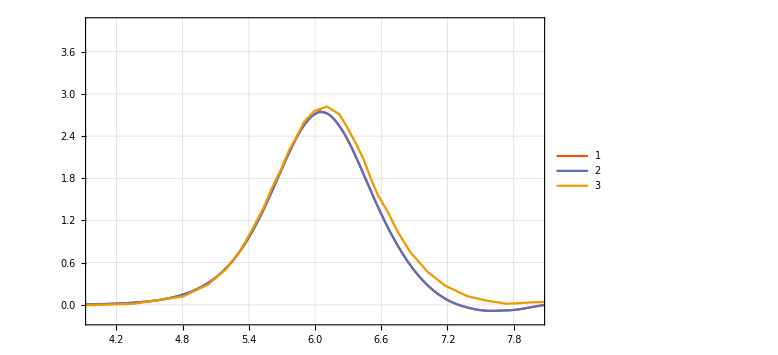

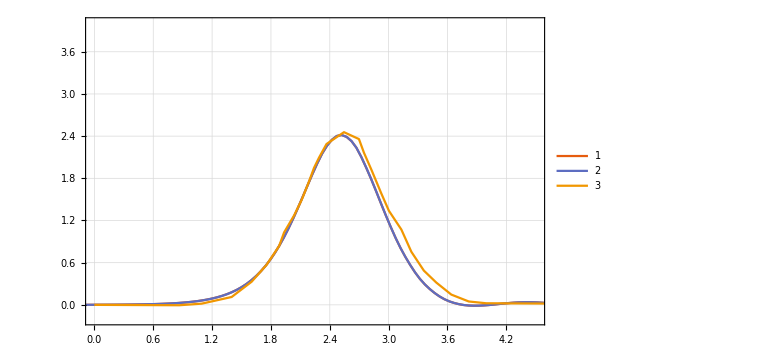

```mathematica
gauge1EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge1.csv"}]];
gauge2EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge2.csv"}]];
gauge3EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge3.csv"}]];

h=0.25;
shiftt1=4.9
shiftt=4.9
ListPlot[
{{importData[jsonLINEAR,"simulation_time"]-shiftt1,(importData[jsonLINEAR,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonLINEAR,"simulation_time"]-shiftt1,(importData[jsonLINEAR,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonLINEAR,"simulation_time"]-shiftt1,(importData[jsonLINEAR,"gauge3_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge3_intersection",3]-h)*100}ᵀ,
gauge1EXP,
gauge2EXP,
gauge3EXP}
,GridLines->Automatic
,PlotStyle->{Red,Red,Red,{Blue,Dashed},{Blue,Dashed},{Blue,Dashed},Gray,Gray,Gray}
(*,Joined->{True,True,True,True,True,True,False,False,False}*)
,PlotLegends->Automatic
,ImageSize->Large
,PlotRange->{{0,15},{-0.2,4}}
,Evaluate[plot2Doption]]

ListPlot[
{{importData[jsonLINEAR,"simulation_time"]-shiftt1,(importData[jsonLINEAR,"gauge3_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge3_intersection",3]-h)*100}ᵀ,
gauge3EXP}
,GridLines->Automatic
(*,Joined->{True,True,True,True,True,True,False,False,False}*)
,PlotLegends->Automatic
,ImageSize->Large
,PlotRange->{{9,15},{-0.2,4}}
,Evaluate[plot2Doption]]

ListPlot[
{{importData[jsonLINEAR,"simulation_time"]-shiftt1,(importData[jsonLINEAR,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge2_intersection",3]-h)*100}ᵀ,
gauge2EXP}
,GridLines->Automatic
(*,Joined->{True,True,True,True,True,True,False,False,False}*)
,PlotLegends->Automatic
,ImageSize->Large
,PlotRange->{{4,8},{-0.2,4}}
,Evaluate[plot2Doption]]

ListPlot[
{{importData[jsonLINEAR,"simulation_time"]-shiftt1,(importData[jsonLINEAR,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge1_intersection",3]-h)*100}ᵀ,
gauge1EXP}
,GridLines->Automatic
(*,Joined->{True,True,True,True,True,True,False,False,False}*)
,PlotLegends->Automatic
,ImageSize->Large
,PlotRange->{{0,4.5},{-0.2,4}}
,Evaluate[plot2Doption]]
```

```mathematica
L=15
1000*9*6*Sum[Sum[Sum[Sum[1,{j,-k,k}],{k,0,L}],{m,-n,n}],{n,0,L}]

10*L^2
```

15

3538944000

2250

```mathematica
./fast./input_files/Ruehl2016_DT0d1_MESHwater0d1.obj_ELEMlinear_ALElinear_ALEPERIOD1
./fast./input_files/Ruehl2016_DT0d1_MESHwater0d1.obj_ELEMlinear_ALEpseudo_quad_ALEPERIOD1
./fast./input_files/Ruehl2016_DT0d1_MESHwater0d1.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1
./fast./input_files/Ruehl2016_DT0d1_MESHwater0d1.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1
を計算中
というのも細かすぎて0.075は，ELEMlinear_ALElinearでも精確だった．．．
```

```mathematica
Clear["Global`*"];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
trial="Trial09"
{jsonInfo[LL="/Volumes/home/BEM/benchmark20250501/Ruehl2016_DT0d1_MESHwater0d15.obj_ELEMlinear_ALElinear_ALEPERIOD1_"<>trial<>"/result.json"],
jsonInfo[LP="/Volumes/home/BEM/benchmark20250501/Ruehl2016_DT0d1_MESHwater0d15.obj_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_"<>trial<>"/result.json"],
jsonInfo[PL="/Volumes/home/BEM/benchmark20250501/Ruehl2016_DT0d1_MESHwater0d15.obj_ELEMpseudo_quad_ALElinear_ALEPERIOD1_"<>trial<>"/result.json"],
jsonInfo[PP="/Volumes/home/BEM/benchmark20250501/Ruehl2016_DT0d1_MESHwater0d15.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_"<>trial<>"/result.json"]}
Import::nffil: "\!\(\*RowBox[{\"Import\"}]\)の最中にファイル\!\(\*RowBox[{\"\\\"/Volumes/home/BEM/benchmark20250501/Ruehl2016_DT0d1_MESHwater0d15.obj_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_Trial08/result.json\\\"\"}]\)が見付かりませんでした．"
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

Trial09

{no. | title | length
1 | cpu_time | 419
2 | eq_of_motion | 419
3 | gradPhi_worst_grad | 419
4 | gradPhi_worst_iteration | 419
5 | gradPhi_worst_value | 419
6 | simulation_time | 419
7 | wall_clock_time | 419
8 | water_E | 419
9 | water_EK | 419
10 | water_EP | 419
11 | water_face_size | 419
12 | water_point_size | 419
13 | water_volume | 419
14 | wg3_intersection | 419
15 | wg6_intersection | 419,no. | title | length
1 | cpu_time | 432
2 | eq_of_motion | 432
3 | gradPhi_worst_grad | 432
4 | gradPhi_worst_iteration | 432
5 | gradPhi_worst_value | 432
6 | simulation_time | 432
7 | wall_clock_time | 432
8 | water_E | 432
9 | water_EK | 432
10 | water_EP | 432
11 | water_face_size | 432
12 | water_point_size | 432
13 | water_volume | 432
14 | wg3_intersection | 432
15 | wg6_intersection | 432,no. | title | length
1 | cpu_time | 321
2 | eq_of_motion | 321
3 | gradPhi_worst_grad | 321
4 | gradPhi_worst_iteration | 321
5 | gradPhi_worst_value | 321
6 | simulation_time | 321
7 | wall_clock_time | 321
8 | water_E | 321
9 | water_EK | 321
10 | water_EP | 321
11 | water_face_size | 321
12 | water_point_size | 321
13 | water_volume | 321
14 | wg3_intersection | 321
15 | wg6_intersection | 321,no. | title | length
1 | cpu_time | 433
2 | eq_of_motion | 433
3 | gradPhi_worst_grad | 433
4 | gradPhi_worst_iteration | 433
5 | gradPhi_worst_value | 433
6 | simulation_time | 433
7 | wall_clock_time | 433
8 | water_E | 433
9 | water_EK | 433
10 | water_EP | 433
11 | water_face_size | 433
12 | water_point_size | 433
13 | water_volume | 433
14 | wg3_intersection | 433
15 | wg6_intersection | 433}

`2`の最中にファイル`1`が見付かりませんでした．

2.

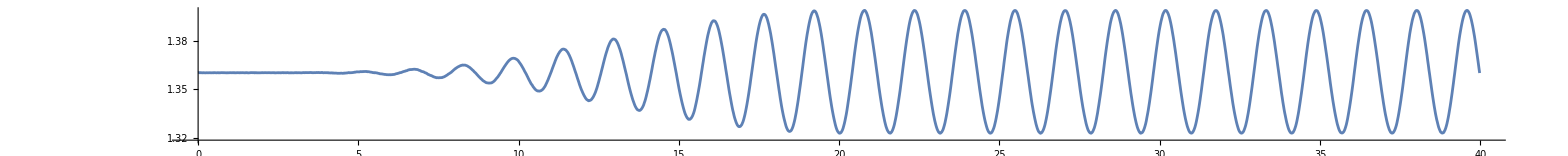

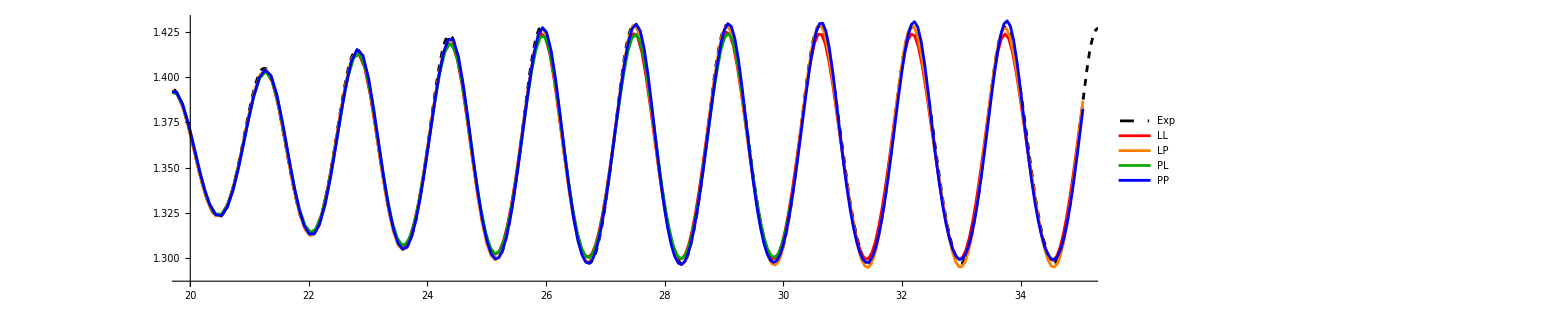

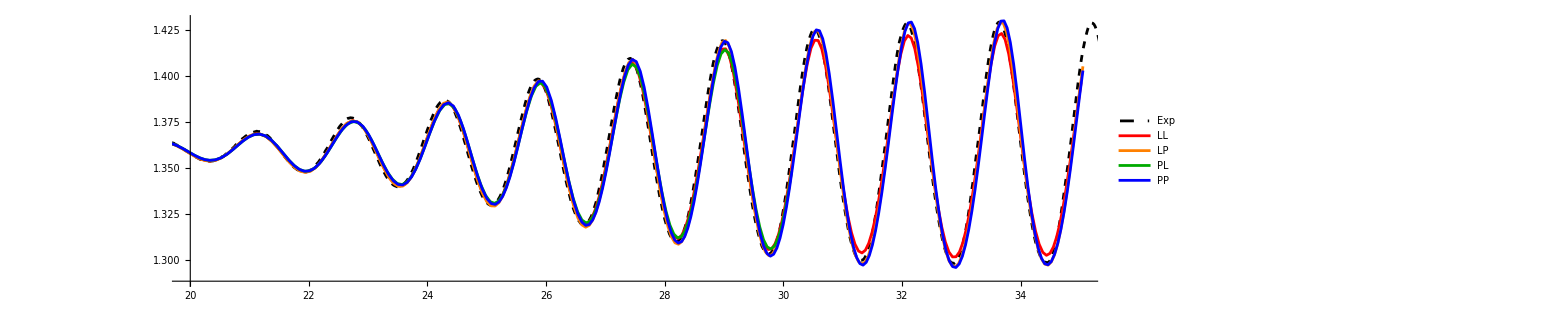

```mathematica
h=1.36;
import[filename_]:=Module[{lines,dataStart},
(*lines=Import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial01/time.txt","Lines"];*)
lines=Import[filename,"Lines"];
(*"% [Data]" の行番号を特定*)
dataStart=First@Flatten@Position[lines,"% [Data]"]+1;
(*データ部だけを取得して数値としてインポート*)
Return@ImportString[StringRiffle[lines[[dataStart;;]]],"Table"][[1]];
]

timedata[name_]:=With[{data=import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/data/WECSIM/inter/RegularWaveTuning1/"<>trial<>"/time.txt"][[;;2000]]},
Transpose[{24*60*60*(data-data[[1]]),h+import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/data/WECSIM/inter/RegularWaveTuning1/"<>trial<>"/"<>name<>".txt"][[;;2000]]}]];

s=0;2.
(*s=1.57*)
(*s=1.2*)
ListPlot[
timedata["wmdisp15"]
,Joined->True,AspectRatio->1/10,ImageSize->2000]

ListPlot[
{timedata["wg3"],
Transpose@{importData[LL,"simulation_time"],(importData[LL,"wg3_intersection",3])},
Transpose@{importData[LP,"simulation_time"],(importData[LP,"wg3_intersection",3])},
Transpose@{importData[PL,"simulation_time"],(importData[PL,"wg3_intersection",3])},
Transpose@{importData[PP,"simulation_time"],(importData[PP,"wg3_intersection",3])}},
Joined->True,
PlotStyle->{{Black,Dashed},Red,Orange,Darker@Green,Blue},
PlotRange->{{20,35},Automatic},
AspectRatio->1/5,
PlotLegends->{"Exp","LL","LP","PL","PP"},
ImageSize->2000]

ListPlot[
{timedata["wg6"],
Transpose@{importData[LL,"simulation_time"],(importData[LL,"wg6_intersection",3])},
Transpose@{importData[LP,"simulation_time"],(importData[LP,"wg6_intersection",3])},
Transpose@{importData[PL,"simulation_time"],(importData[PL,"wg6_intersection",3])},
Transpose@{importData[PP,"simulation_time"],(importData[PP,"wg6_intersection",3])}},
Joined->True,
PlotStyle->{{Black,Dashed},Red,Orange,Darker@Green,Blue},
PlotRange->{{20,35},Automatic},
AspectRatio->1/5,
PlotLegends->{"Exp","LL","LP","PL","PP"},
PlotRange->All,
ImageSize->2000]
```

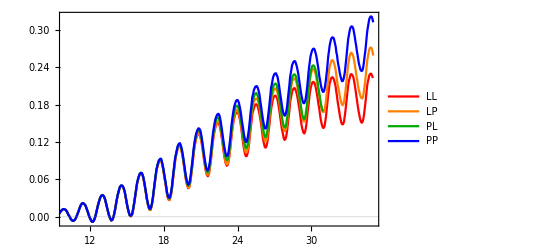

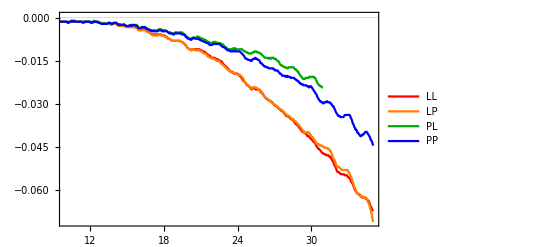

```mathematica
Eerror[json_]:=Transpose@With[{data=importData[json,"water_EK"]+importData[json,"water_EP"],time=importData[json,"simulation_time"]},{time,100*(data/data[[1]]-1)}];
Verror[json_]:=Transpose@With[{data=importData[json,"water_volume"],time=importData[json,"simulation_time"]},{time,100*(data/data[[1]]-1)}];

ListPlot[{Eerror[LL],Eerror[LP],Eerror[PL],Eerror[PP]},
PlotStyle->{Red,Orange,Darker@Green,Blue},
PlotRange->{{10,35},All},
plot2Doption,PlotRange->All,PlotLegends->{"LL","LP","PL","PP"}]

ListPlot[{Verror[LL],Verror[LP],Verror[PL],Verror[PP]},
PlotStyle->{Red,Orange,Darker@Green,Blue},
PlotRange->{{10,35},All},
plot2Doption,PlotRange->All,PlotLegends->{"LL","LP","PL","PP"}]
```

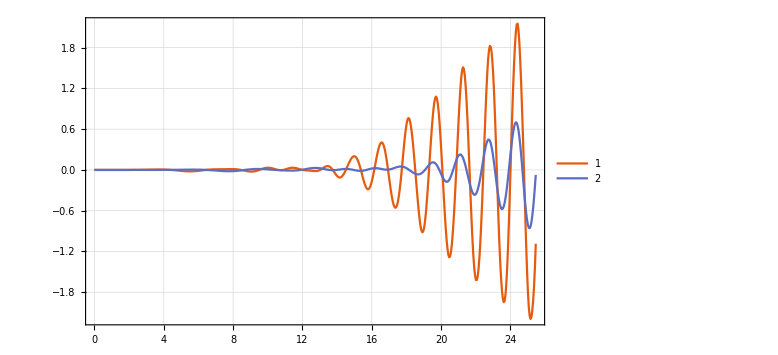

```mathematica
ListPlot[
{Transpose@{importData[jsonQUAD,"simulation_time"],(importData[jsonQUAD,"wg3_intersection",3]-h)*100},
Transpose@{importData[jsonQUAD,"simulation_time"],(importData[jsonQUAD,"wg6_intersection",3]-h)*100}}
,GridLines->Automatic
(*,Joined->{True,True,True,True,True,True,False,False,False}*)
,PlotRange->All
,PlotLegends->Automatic
,ImageSize->Large
,Evaluate[plot2Doption]]
```